```mathematica
ep=0.008;β=0.7;γ=0.8;maxtime=20;
α=0.55;γt=1/α+5;
xmin=-40;xmax=40;ρ=0;
g[v_]=v(1-v)(v-α)-(1+α-3v)ρ^2/2;
eqn=FindRoot[g[v]==0,{v,-0.1}];
v0=v/.eqn;
f[v_]=g[v0+v]-g[v0];
δ=0.3;
Print["delta min: ",1/(α γt)]
-f'[0]-δ/γt
(*Design Parameters*)
MM=0.05;maxtime2=4.8;switchingTime=-5;
leftBoundaryTime=-10;
leftBoundaryTime2=-12;
```

delta min: 0.266667

0.506

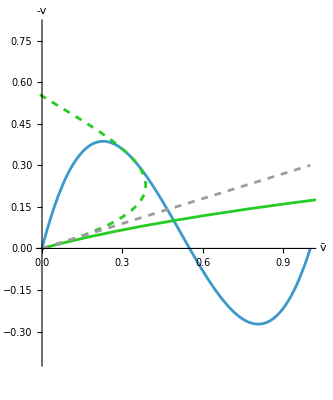

```mathematica
g1=ParametricPlot[{x,-γt f[x]},{x,0,1},AxesLabel->{"v̄","-v"}];
g2=ParametricPlot[{γt f[-y],y},{y,0,1},PlotStyle->StandardGreen];
g2b=ParametricPlot[{-γt f[y],y},{y,0,1},PlotStyle->{StandardGreen,Dashed}];
g3=ParametricPlot[{x,δ x},{x,0,1},PlotStyle->{StandardGray,Dashed}];

Show[g1,g2,g2b,g3,PlotRange->{{0,1},{-0.4,0.8}}]
```

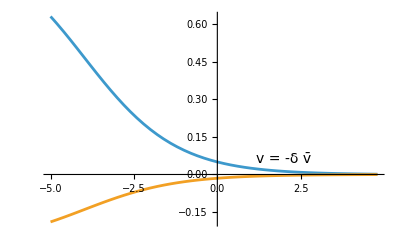

0.62994

```mathematica
bestdy=0;
bestvalue=5;
Do[
{V1}=NDSolveValue[{v1''[x]==-f[v1[x]]- δ v1[x]/γt, v1[0]==MM,v1'[0]==-MM Sqrt[-f'[0]-δ/γt]+dy},{v1},{x,0,maxtime2}];
(*Plot[V1[x],{x,0,maxtime2}]*)
If[V1[maxtime2]>0&&V1[maxtime2]^2+V1'[maxtime2]^2<bestvalue,bestdy=dy;bestvalue=V1[maxtime2]^2+V1'[maxtime2]^2];
,{dy,-0.01,0.01,0.00001}]
(*bestdy
-MM Sqrt[-f'[0]-δ/γt]+bestdy*)

{V1}=NDSolveValue[{v1''[x]==-f[v1[x]]- δ v1[x]/γt, v1[0]==MM,v1'[0]==-MM Sqrt[-f'[0]-δ/γt]+bestdy},{v1},{x,switchingTime,maxtime2}];
g1=Plot[{V1[x],-δ V1[x]},{x,switchingTime,maxtime2},PlotRange->All];
labels=Graphics[{
Text[Style["v = -δ v̄",FontSize->14],{2,0.06},{0,0}]
}];
Show[g1,labels]
V1[switchingTime]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

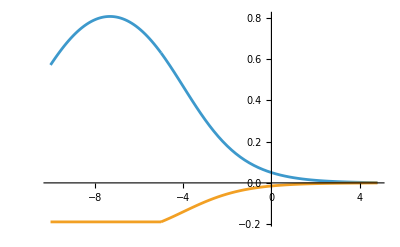

0.62994

0.188982

```mathematica
{V1b,V2b}=NDSolveValue[{v1''[x]==-f[v1[x]]+ v2[x]/γt,
v2''[x]==0,(*-f[v2[x]]+0.2v1[x]/γt,*)
v1[switchingTime]==V1[switchingTime],
v2[switchingTime]==-δ V1[switchingTime],
v1'[switchingTime]==V1'[switchingTime],(*V1'[switchingTime],*)
v2'[switchingTime]==0},{v1,v2},{x,leftBoundaryTime,0}]
(*ParametricPlot[{V[x],U[x]},{x,-5,3},PlotRange->{{-0.2,0.2},{-0.2,0.2}}]*)
g1=Plot[{V1[x],-δ V1[x]},{x,switchingTime,maxtime2},PlotRange->All];
g2=Plot[{V1b[x],V2b[x]},{x,leftBoundaryTime,switchingTime}];
labels=Graphics[{
Text[Style["v''[x] = -f[v]+0.2v̄[x]/γ",FontSize->14],{-2.5,0.02},{0,0}]
}];
Show[g1,g2,PlotRange->All]
V1[switchingTime]
-V2b[leftBoundaryTime]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

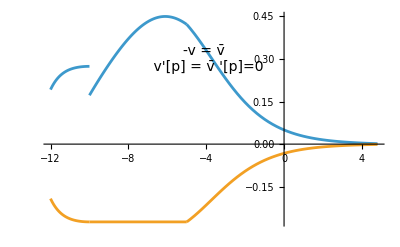

```mathematica
{V1c,V2c}=NDSolveValue[{v1''[x]==-f[v1[x]]+v2[x]/γt,v2''[x]==-f[v2[x]]+v1[x]/γt,
v1[leftBoundaryTime]==-V2b[leftBoundaryTime],
v1'[leftBoundaryTime]==0,
v2[leftBoundaryTime]==V2b[leftBoundaryTime],
v2'[leftBoundaryTime]==0
},{v1,v2},{x,leftBoundaryTime2,leftBoundaryTime}]
(*ParametricPlot[{V[x],U[x]},{x,-5,3},PlotRange->{{-0.2,0.2},{-0.2,0.2}}]*)
g1=Plot[{V1[x],-δ V1[x]},{x,switchingTime,maxtime2}];
g2=Plot[{V1b[x],V2b[x]},{x,leftBoundaryTime,switchingTime}];
g3=Plot[{V1c[x],-V1c[x]},{x,leftBoundaryTime2,leftBoundaryTime}];
labels=Graphics[{
Text[Style["-v = v̄ \n v'[p] = v̄ '[p]=0",FontSize->14],{-4,0.3},{0,0}]
}];
Show[g1,g2,g3,labels,PlotRange->All]
```

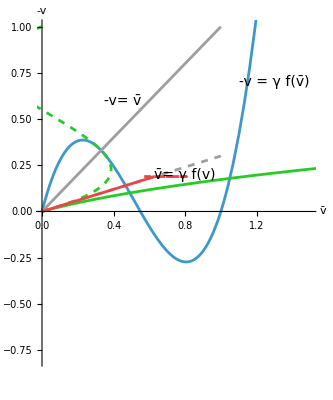

```mathematica
g1=ParametricPlot[{x,-γt f[x]},{x,0,1.5},AxesLabel->{"v̄","-v"}];
g2=ParametricPlot[{γt f[-y],y},{y,0,1},PlotStyle->StandardGreen];
g2b=ParametricPlot[{-γt f[y],y},{y,0,1},PlotStyle->{StandardGreen,Dashed}];
g3=ParametricPlot[{{x,δ x},{x,x}},{x,0,1},PlotStyle->{{StandardGray,Dashed},{StandardGray}}];
(*c[x_]=Which[x<0,{V1[x],-δ V1[x]},True,{V1b[x],V2b[x]}];*)
g4=ParametricPlot[{V1[x],δ V1[x]},{x,switchingTime,maxtime2},PlotStyle->{StandardRed}];
g4b=ParametricPlot[{V1b[x],-V2b[x]},{x,leftBoundaryTime,switchingTime},PlotStyle->{StandardRed,Dashed}];

(*g4c=ParametricPlot[{V1c[x],V1c[x]},{x,leftBoundaryTime2,leftBoundaryTime},PlotStyle->StandardRed];*)
labels=Graphics[{
Text[Style["-v = γ f(v̄)",FontSize->14],{1.3,0.7},{0,0}],
(*Text[Style["-v= δ v̄",FontSize->14],{0.8,0.4},{0,0}],*)
Text[Style["-v= v̄",FontSize->14],{0.45,0.6},{0,0}],
Text[Style["v̄= γ f(v)",FontSize->14],{0.8,0.2},{0,0}]
}
];

Show[g1,g2,g2b,g3,g4,g4b,labels,PlotRange->{{0,1.5},{-0.8,1}}]
```